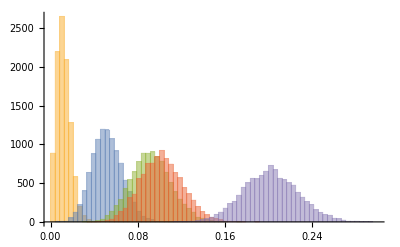

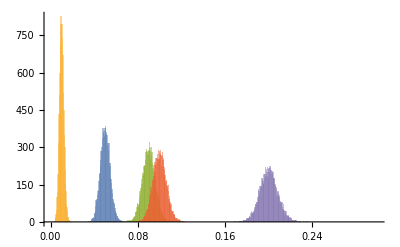

```mathematica
c=30;samples[p_]:=Table[Mean[RandomVariate[BernoulliDistribution[p],8c]],{n,1,10000}];
Histogram[samples[#]&/@{0.01,0.05,0.09,0.1,0.2},{0,0.3,1/(8c)}]
c=300;samples[p_]:=Table[Mean[RandomVariate[BernoulliDistribution[p],8c]],{n,1,10000}];
Histogram[samples[#]&/@{0.01,0.05,0.09,0.1,0.2},{0,0.3,1/(8c)}]
```

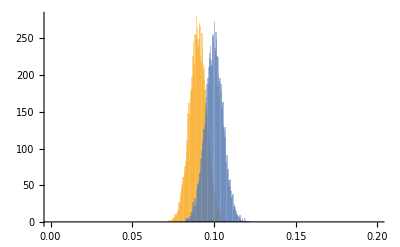

```mathematica
c=3000;samples[p_]:=Table[Mean[RandomVariate[BernoulliDistribution[p],c]],{n,1,10000}];
Histogram[samples[#]&/@{0.09,0.1},{0,0.2,1/c}]
```

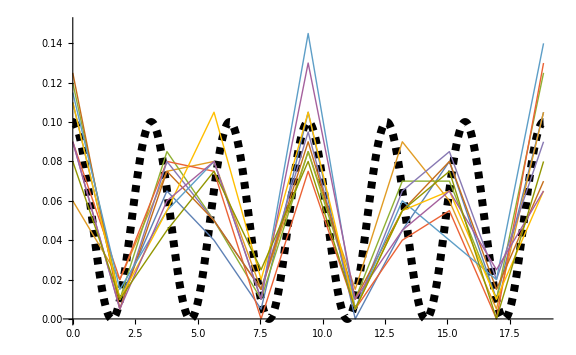

```mathematica
c=.;
oscillation[c_,n_,tMax_]:={#,Mean[RandomVariate[BernoulliDistribution[0.1 Cos[#]^2],c]]}&/@Range[0,tMax,tMax/n]
(Show[Plot[0.1 Cos[t]^2,{t,0,#},PlotRange->{0,0.15},PlotStyle->{Thickness[0.01],Dashed,Black}],ListPlot[Table[oscillation[200,10,#],{n,1,10}],Joined->True,PlotStyle->Thick],ImageSize->Large])&/@{6π}
```

1600

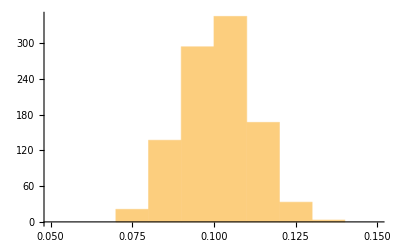
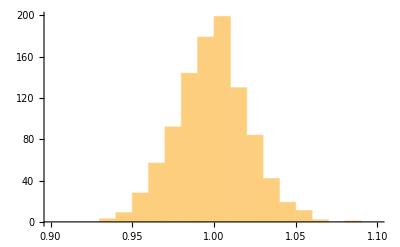

```mathematica
c=100;n=16;
c n
fit=Table[{a,b}/.FindFit[oscillation[c,n],a Cos[b t]^2,{a,b},t],{i,1,1000}];
{Histogram[fit[[All,1]],{0.05,.15,1/c}],Histogram[fit[[All,2]],{0.9,1.1,1/c}]}
```

2400

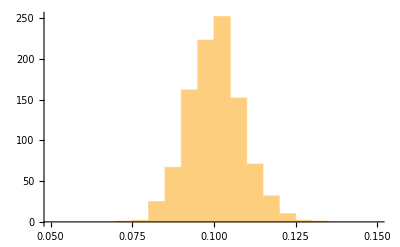
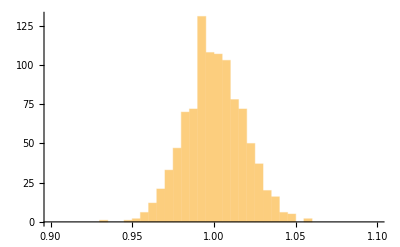

```mathematica
c=200;n=12;
c n
fit=Table[{a,b}/.FindFit[oscillation[c,n],a Cos[b t]^2,{a,b},t],{i,1,1000}];
{Histogram[fit[[All,1]],{0.05,.15,1/c}],Histogram[fit[[All,2]],{0.9,1.1,1/c}]}
```

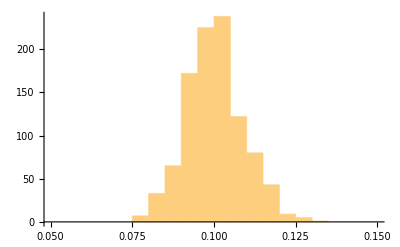
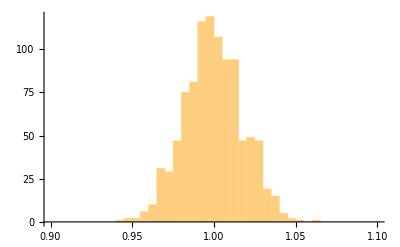

```mathematica
c=200;n=12;tMax=2π;
fit=Table[{a,b}/.FindFit[oscillation[c,n,tMax],a Cos[b t]^2,{a,b},t],{i,1,1000}];
{Histogram[fit[[All,1]],{0.05,.15,1/c}],Histogram[fit[[All,2]],{0.9,1.1,1/c}]}
```

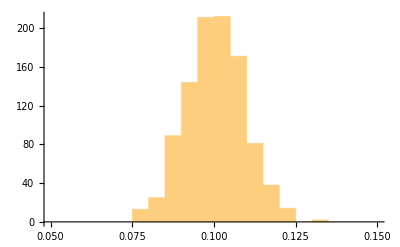
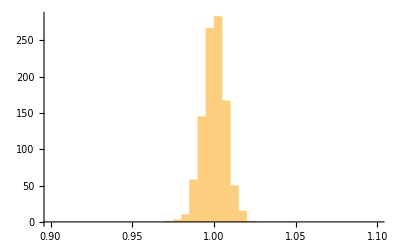

```mathematica
c=200;n=12;tMax=4π;
fit=Table[{a,b}/.FindFit[oscillation[c,n,tMax],a Cos[b t]^2,{a,b},t],{i,1,1000}];
{Histogram[fit[[All,1]],{0.05,.15,1/c}],Histogram[fit[[All,2]],{0.9,1.1,1/c}]}
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

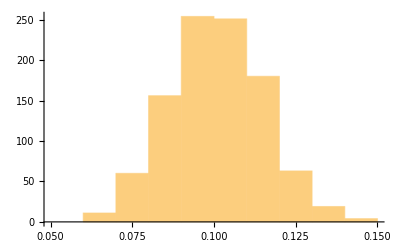
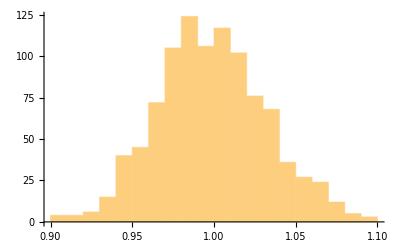

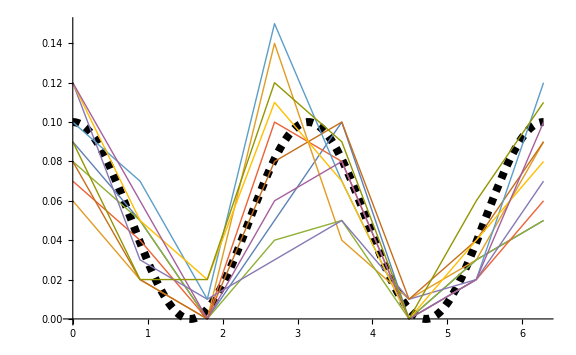

```mathematica
c=100;n=7;tMax=2π;
fit=Table[{a,b}/.FindFit[oscillation[c,n,tMax],a Cos[b t]^2,{a,b},t],{i,1,1000}];
{Histogram[fit[[All,1]],{0.05,.15,1/c}],Histogram[fit[[All,2]],{0.9,1.1,1/c}]}
Show[Plot[0.1 Cos[t]^2,{t,0,tMax},PlotRange->{0,0.15},PlotStyle->{Thickness[0.01],Dashed,Black}],ListPlot[Table[oscillation[c,n,tMax],{i,1,10}],Joined->True,PlotStyle->Thick],ImageSize->Large]
```

```mathematica
π/2//N
```

1.5708

```mathematica
4
```

```mathematica
Range[0,tMax,tMax/8]//Length
```

9

```mathematica
1/(1000 10^-6)//N
```

1000.

```mathematica
1/(2π 28 10^-6)//N
```

5684.11

```mathematica
1/(2π  120 10^-6)//N
```

1326.29

```mathematica
119/28.7
```

4.14634

```mathematica
11/4.14
```

2.657

```mathematica
30/4.14
```

7.24638

{a→0.199546,b→0.049809,c→0.341111}

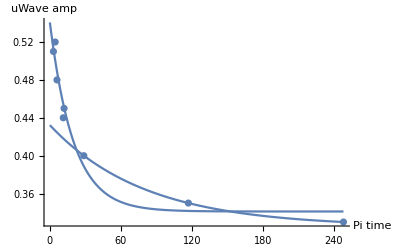

```mathematica
amps={51,48,44,52,45,40,35,33}1/100;
times={3,6,11.3,4.5,12,28.7,117,248};
data=Transpose@{times,amps};
{a,b,c,t,d}=.;f=FindFit[data,a Exp[-b t]+c,{a,b,c},t]
lp=Show[Plot[(a Exp[-b t]+c/.#)&/@{f,f2},{t,0,Max[times]},PlotRange->{32,55}1/100],ListPlot[data],PlotRange->All,AxesLabel->{"Pi time","uWave amp"}]
```

```mathematica
1/(π 119 10^-6)//N
```

2674.87

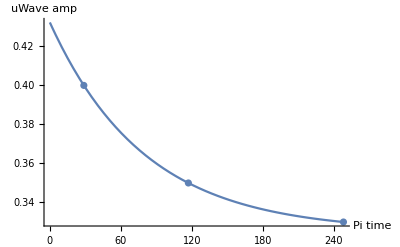

```mathematica
amps={40,35,33}1/100;
times={28.7,117,248};
data=Transpose@{times,amps};
{a,b,c,t,d}=.;f2=FindFit[data,a Exp[-b t]+c,{{a,0.2},{b,0.05},{c,.32}},t];
lp=Show[Plot[a Exp[-b t]+c/.f2,{t,0,Max[times]},PlotRange->{32,55}1/100],ListPlot[data],PlotRange->All,AxesLabel->{"Pi time","uWave amp"}]
```